```mathematica
Clear["Global`*"]
ni=Sqrt[Econst T^3 Exp[(-q VG[T])/(kB T)]];(*ni^2*)
IS=q A/NB ni^2 D/.D->kB T/q μ/.μ->C T^-n;
IC[T_]=IS Exp[q VBE[T]/(kB T)]//Factor;
IC[T];IC[Tr];
ICTR=F Tr^δ/(F T^δ);

Log[IC[Tr]/IC[T]]//Expand;
Solve[IC[Tr]/IC[T]==ICTR,VBE[T],Real][[1,1]]//Simplify//Collect[#,T/Tr]&//TraditionalForm
Solve[IC[Tr]/IC[T]==ICTR,VBE[T],Real][[1,1]]//Simplify//PowerExpand//Collect[#,T/Tr]&//TeXForm
(*Log[Exp[x]]//FullSimplify*)
(*Solve[{==ICTR},VBE[T]]//ExpandAll
```

Solve::bdomv: Warning: Real is not a valid domain specification. Assuming it is a variable to eliminate.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

VBE(T)→-(kB T log(T^(-δ-n+4) Tr^(δ+n-4)))/q+(T (VBE(Tr)-VG(Tr)))/Tr+VG(T)

Solve::bdomv: Warning: Real is not a valid domain specification. Assuming it is a variable to eliminate.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

\text{VBE}(T)\to -\frac{\text{kB} T ((-\delta -n+4) \log (T)+(\delta +n-4) \log
   (\text{Tr}))}{q}+\frac{T
   (\text{VBE}(\text{Tr})-\text{VG}(\text{Tr}))}{\text{Tr}}+\text{VG}(T)

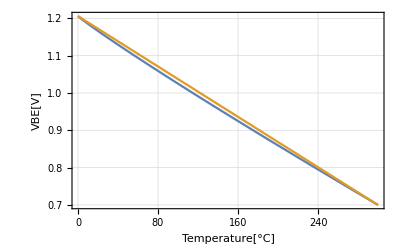

```mathematica
VEB[T_]=VGT0+T/T0 (VEBT0-VGT0)-(η-m) (kB T)/e Log[T/T0]/.VGT0->1.206/.T0->300/.VEBT0->0.7/.η->1/.m->2.3/.kB/e->0.00008633333333333334;
Plot[{VEB[T],VGT0+T/T0 (VEBT0-VGT0)/.VGT0->1.206/.T0->300/.VEBT0->0.7},{T,0,300},Frame->True,GridLines->Automatic,FrameLabel->{"Temperature[°C]","VBE[V]"}]
```

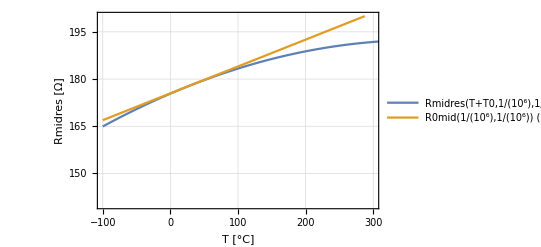

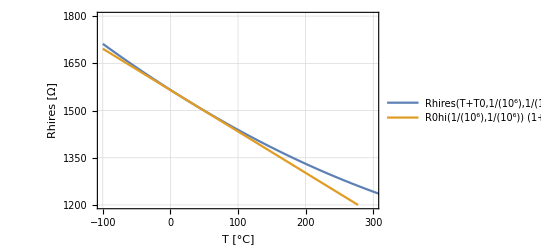

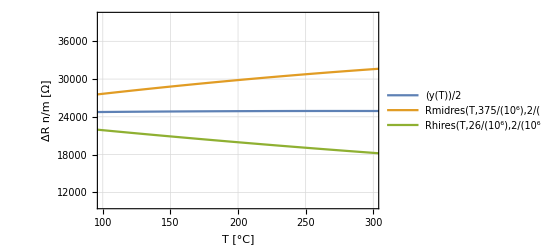

```mathematica
Clear["Global`*"]
R0mid[l_,W_]:=rsh*l/(W-1*10^-7)/.rsh->1.6*10^2(*/.l->10^-6/.W->10^-6*);tc1mid=4.8*10^-4;tc2mid=-7.0*10^-7;
R0hi[l_,W_]:=rsh*l/(W-1.5*10^-7)/.rsh->1.3*10^3(*/.l->10^-6/.W->10^-6*);tc1hi=-8.6*10^-4;tc2hi=6.3*10^-7;
R0mid;R0hi;T0=273.15;
Rmidres[T_,l_,W_]:=R0mid[l,W] (1+tc1mid (T-T0-27)+tc2mid (T-T0-27)^2)
Rhires[T_,l_,W_]:=R0hi[l,W] (1+tc1hi (T-T0-27)+tc2hi (T-T0-27)^2)
Plot[{Rmidres[T+T0,10^-6,10^-6],R0mid[10^-6,10^-6] (1+tc1mid (T-27))},{T,-100,500},PlotRange->{{-100,300},{140,200}},Frame->True,GridLines->Automatic,FrameLabel->{Style[T"[°C]"(*,Large,Bold,Blue*)],Style[Rmidres"[Ω]"(*,Large,Bold,Blue*)]},PlotLegends->"Expressions"]
Plot[{Rhires[T+T0,10^-6,10^-6],R0hi[10^-6,10^-6] (1+tc1hi (T-27))},{T,-100,500},PlotRange->{{-100,300},{1200,1800}},Frame->True,GridLines->Automatic,FrameLabel->{Style[T"[°C]"(*,Large,Bold,Blue*)],Style[Rhires"[Ω]"(*,Large,Bold,Blue*)]},PlotLegends->"Expressions"]
(*Plot[8.3 Rmidres[T+273.15]-Rhires[T+273.15],{T,-100,500},PlotRange->{{-100,300},{-400,400}},Frame->True,GridLines->Automatic,FrameLabel->{Style[T"[°C]",Large,Bold,Blue],Style[ΔR"[Ω]",Large,Bold,Blue]}]*)
y[x_]:=n Rmidres[x,375 10^-6,2 10^-6]+m Rhires[x,26 10^-6,2 10^-6]/.n->1/.m->1
(*Plot[Solve[y'[x]==0,a][[1,1,2]],{x,0,500}];*)
(*Plot[{Rmidres[T,375 10^-6,2 10^-6],Rhires[T,26 10^-6,2 10^-6]},{T,-100,500}]*)
Plot[{y[T]/2,Rmidres[T,375 10^-6,2 10^-6],Rhires[T,26 10^-6,2 10^-6](*,y[T,2,1],y[T,3,1],y[T,5,1],y[T,10,1]*)},{T,-100,500},PlotRange->{{100,300},{10000,40000}},Frame->True,GridLines->Automatic,FrameLabel->{Style[T"[°C]",Large,Bold,Blue],Style["n/m" ΔR"[Ω]",Large,Bold,Blue]},PlotLegends->"Expressions"]
```

## 宽温度范围下阻值的调整

```mathematica
Clear["Global`*"];
R0mid[l_,W_]:=rsh*l/(W-1*10^-7)/.rsh->1.6*10^2(*/.l->10^-6/.W->10^-6*);tc1mid=4.8*10^-4;tc2mid=-7.0*10^-7;
R0hi[l_,W_]:=rsh*l/(W-1.5*10^-7)/.rsh->1.3*10^3(*/.l->10^-6/.W->10^-6*);tc1hi=-8.6*10^-4;tc2hi=6.3*10^-7;
R0mid;R0hi;T0=273.15;
Rmidres[T_,l_,W_]:=R0mid[l,W] (1+tc1mid (T-T0-27)+tc2mid (T-T0-27)^2)
Rhires[T_,l_,W_]:=R0hi[l,W] (1+tc1hi (T-T0-27)+tc2hi (T-T0-27)^2)
totalR[T_,n_,m_]:=Rmidres[T,n 10^-6,2 10^-6]+Rhires[T,m 10^-6,2 10^-6](*/.l->10^-6/.W->10^-6*)
(*Plot[{totalR[T,375,26],y[T]},{T,100,300}];D[totalR[T,m,n],T]==0*)
Manipulate[Plot[{totalR[T,n,m],totalR[T,375,26],Rmidres[T,n 10^-6,2 10^-6],Rhires[T,m 10^-6,2 10^-6]},{T,0,300},PlotRange->{0,60000},Frame->True,GridLines->Automatic,FrameLabel->{Style[T"[°C]"],Style[total_R"[Ω]"]},PlotLegends->{"totalR","totalR[375,26]","Rmidres","Rhires"}],{{n,1,"number of blocks in midR(n)"},1,500},{{m,1,"number of blocks in hiR(m)"},1,100}]
```

```mathematica
D[totalR[T,n,m],T]//Collect[#,T]&
Solve[-0.8700787567567567 m+0.07580715789473684 n==0,m][[1,1]]
Solve[0.0008854054054054055 m-0.00011789473684210524 n==0,m][[1,1]]
```

-0.870079 m+0.0758072 n+(0.000885405 m-0.000117895 n) T

m→0.0871268 n

m→0.133153 n

```mathematica
hamiltonian[V_]@psi_:=-h^2/(2 m) D[psi,{x,2}]+V psi
hamiltonian[V0]@(E^(I k x))//Collect[#,E^(I k x)]&
```

ⅇ^(ⅈ k x) ((h^2 k^2)/(2 m)+V0)

```mathematica
#^3&@x
```

x^3

```mathematica
Concentration[ConG_]@ConC_:=DifCoef D[ConC[z],{z,2}]-2 (kcat Et ConG)/(Km+ConG)
```

```mathematica
f[x_,y_]:=x^2+y^2
f[x_]@y_:=x^2+y^2
Integrate[x^2+x+1,x,GeneratedParameters->C]
```

x+x^2/2+x^3/3+C[1]

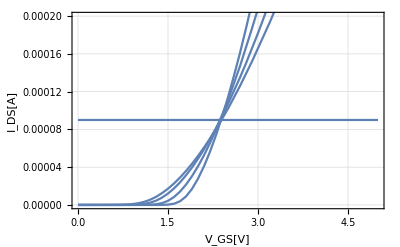

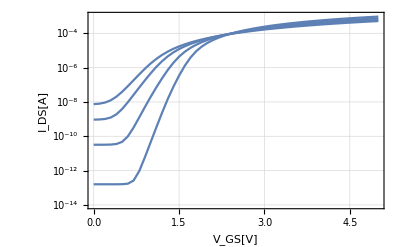

```mathematica
W6temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp30_ids.txt","Table"]];
W6logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
W6temp130=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp130_ids.txt","Table"]];
W6logtemp130=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp130_ids.txt","Table"],Joined->True];
W6temp230=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp230_ids.txt","Table"]];
W6logtemp230=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp230_ids.txt","Table"],Joined->True];
W6temp80=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp80_ids.txt","Table"]];
W6logtemp80=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp80_ids.txt","Table"],Joined->True];
W6temp180=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp180_ids.txt","Table"]];
W6logtemp180=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp180_ids.txt","Table"],Joined->True];
W6temp280=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp280_ids.txt","Table"]];
W6logtemp280=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp280_ids.txt","Table"],Joined->True];
W6temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp300_ids.txt","Table"]];
W6logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW6u/temp300_ids.txt","Table"],Joined->True];
W6stand=ListLinePlot[{{0,90 10^-6},{5,90 10^-6}}];
Show[W6stand,W6temp30,(*temp80,*)W6temp130,(*temp180,*)W6temp230,(*temp280,*)W6temp300,PlotRange->{0,0.0002},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[W6logtemp30,W6logtemp130,W6logtemp230,W6logtemp300,W6stand,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

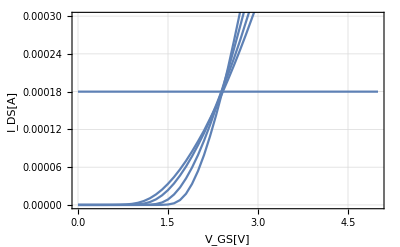

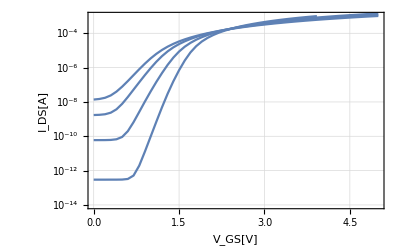

```mathematica
W12temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp30_ids.txt","Table"]];
W12logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
W12temp130=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp130_ids.txt","Table"]];
W12logtemp130=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp130_ids.txt","Table"],Joined->True];
W12temp230=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp230_ids.txt","Table"]];
W12logtemp230=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp230_ids.txt","Table"],Joined->True];
W12temp80=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp80_ids.txt","Table"]];
W12logtemp80=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp80_ids.txt","Table"],Joined->True];
W12temp180=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp180_ids.txt","Table"]];
W12logtemp180=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp180_ids.txt","Table"],Joined->True];
W12temp280=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp280_ids.txt","Table"]];
W12logtemp280=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp280_ids.txt","Table"],Joined->True];
W12temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp300_ids.txt","Table"]];
W12logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW12u/temp300_ids.txt","Table"],Joined->True];
W12stand=ListLinePlot[{{0,180 10^-6},{5,180 10^-6}}];
Show[W12stand,W12temp30,(*temp80,*)W12temp130,(*temp180,*)W12temp230,(*temp280,*)W12temp300,PlotRange->{0,0.0003},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[W12logtemp30,W12logtemp130,W12logtemp230,W12logtemp300,W12stand,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

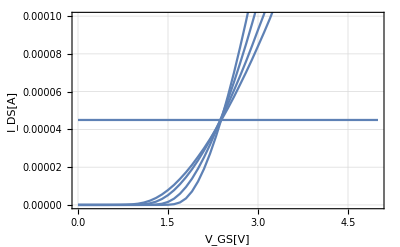

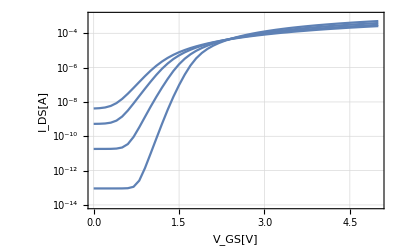

```mathematica
W3temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp30_ids.txt","Table"]];
W3logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
W3temp130=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp130_ids.txt","Table"]];
W3logtemp130=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp130_ids.txt","Table"],Joined->True];
W3temp230=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp230_ids.txt","Table"]];
W3logtemp230=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp230_ids.txt","Table"],Joined->True];
W3temp80=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp80_ids.txt","Table"]];
W3logtemp80=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp80_ids.txt","Table"],Joined->True];
W3temp180=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp180_ids.txt","Table"]];
W3logtemp180=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp180_ids.txt","Table"],Joined->True];
W3temp280=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp280_ids.txt","Table"]];
W3logtemp280=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp280_ids.txt","Table"],Joined->True];
W3temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp300_ids.txt","Table"]];
W3logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW3u/temp300_ids.txt","Table"],Joined->True];
W3stand=ListLinePlot[{{0,45 10^-6},{5,45 10^-6}}];
Show[W3stand,W3temp30,(*temp80,*)W3temp130,(*temp180,*)W3temp230,(*temp280,*)W3temp300,PlotRange->{0,0.0001},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[W3logtemp30,W3logtemp130,W3logtemp230,W3logtemp300,W3stand,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

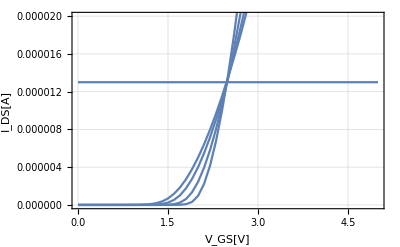

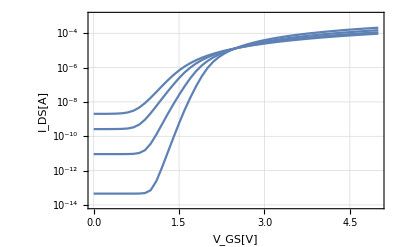

```mathematica
W1temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp30_ids.txt","Table"]];
W1logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
W1temp130=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp130_ids.txt","Table"]];
W1logtemp130=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp130_ids.txt","Table"],Joined->True];
W1temp230=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp230_ids.txt","Table"]];
W1logtemp230=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp230_ids.txt","Table"],Joined->True];
W1temp80=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp80_ids.txt","Table"]];
W1logtemp80=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp80_ids.txt","Table"],Joined->True];
W1temp180=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp180_ids.txt","Table"]];
W1logtemp180=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp180_ids.txt","Table"],Joined->True];
W1temp280=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp280_ids.txt","Table"]];
W1logtemp280=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp280_ids.txt","Table"],Joined->True];
W1temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp300_ids.txt","Table"]];
W1logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L1uW1u/temp300_ids.txt","Table"],Joined->True];
W1stand=ListLinePlot[{{0,13 10^-6},{5,13 10^-6}}];
Show[W1stand,W1temp30,(*temp80,*)W1temp130,(*temp180,*)W1temp230,(*temp280,*)W1temp300,PlotRange->{0,0.00002},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[W1logtemp30,W1logtemp130,W1logtemp230,W1logtemp300,W1stand,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

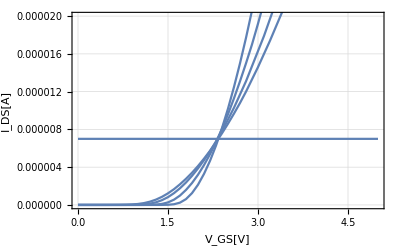

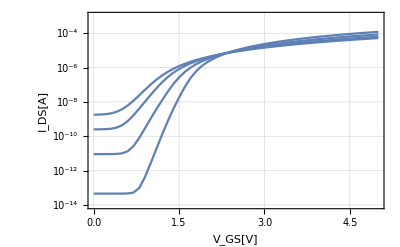

```mathematica
L3W1temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp30_ids.txt","Table"]];
L3W1logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L3W1temp130=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp130_ids.txt","Table"]];
L3W1logtemp130=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp130_ids.txt","Table"],Joined->True];
L3W1temp230=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp230_ids.txt","Table"]];
L3W1logtemp230=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp230_ids.txt","Table"],Joined->True];
L3W1temp80=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp80_ids.txt","Table"]];
L3W1logtemp80=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp80_ids.txt","Table"],Joined->True];
L3W1temp180=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp180_ids.txt","Table"]];
L3W1logtemp180=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp180_ids.txt","Table"],Joined->True];
L3W1temp280=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp280_ids.txt","Table"]];
L3W1logtemp280=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp280_ids.txt","Table"],Joined->True];
L3W1temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp300_ids.txt","Table"]];
L3W1logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L3uW1u/temp300_ids.txt","Table"],Joined->True];
L3W1stand=ListLinePlot[{{0,7 10^-6},{5,7 10^-6}}];
Show[L3W1stand,L3W1temp30,(*temp80,*)L3W1temp130,(*temp180,*)L3W1temp230,(*temp280,*)L3W1temp300,PlotRange->{0,0.00002},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[L3W1logtemp30,L3W1logtemp130,L3W1logtemp230,L3W1logtemp300,L3W1stand,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

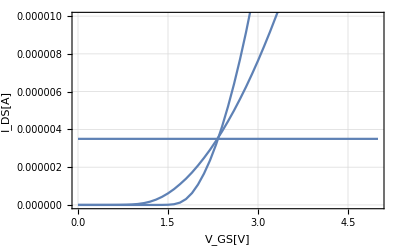

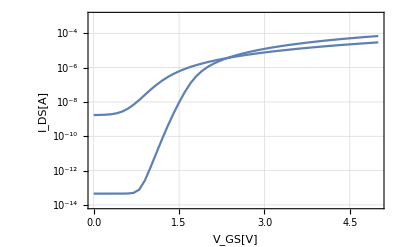

```mathematica
Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L6uW1u/temp30_ids.txt","Table"];
L6W1temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L6uW1u/temp30_ids.txt","Table"]];
L6W1logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L6uW1u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L6W1temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L6uW1u/temp300_ids.txt","Table"]];
L6W1logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L6uW1u/temp300_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L6W1stand=ListLinePlot[{{0,3.5 10^-6},{5,3.5 10^-6}}];
Show[L6W1stand,L6W1temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)L6W1temp300,PlotRange->{0,0.00001},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[L6W1logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)L6W1logtemp300,L6W1stand,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

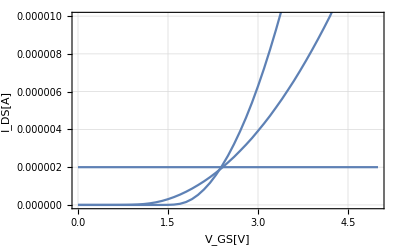

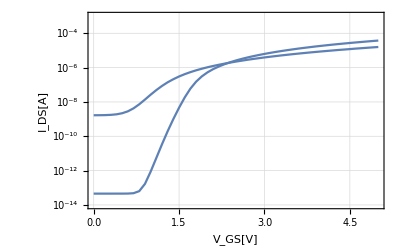

```mathematica
Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L12uW1u/temp30_ids.txt","Table"];
L12W1temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L12uW1u/temp30_ids.txt","Table"]];
L12W1logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L12uW1u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L12W1temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L12uW1u/temp300_ids.txt","Table"]];
L12W1logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L12uW1u/temp300_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.0001}];
L12W1stand=ListLinePlot[{{0,2 10^-6},{5,2 10^-6}}];
Show[L12W1stand,L12W1temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)L12W1temp300,PlotRange->{0,0.00001},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[L12W1logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)L12W1logtemp300,L12W1stand,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

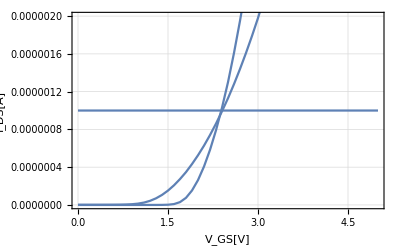

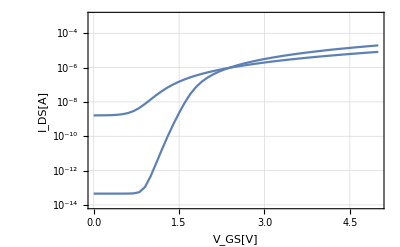

```mathematica
L24W1temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L24uW1u/temp30_ids.txt","Table"]];
L24W1logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L24uW1u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L24W1temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L24uW1u/temp300_ids.txt","Table"]];
L24W1logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L24uW1u/temp300_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L24W1stand=ListLinePlot[{{0,10^-6},{5,10^-6}}];
Show[L24W1stand,L24W1temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)L24W1temp300,PlotRange->{0,0.000002},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[L24W1logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)L24W1logtemp300,L24W1stand,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

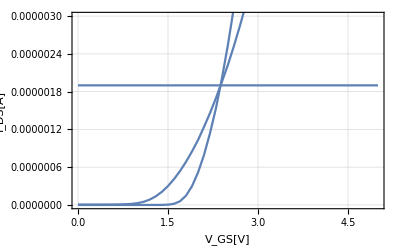

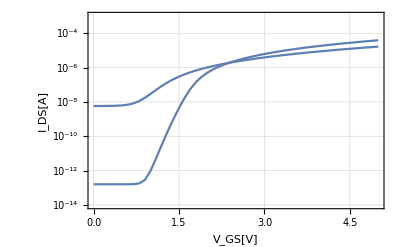

```mathematica
L36W6temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L36uW6u/temp30_ids.txt","Table"]];
L36W6logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L36uW6u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L36W6temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L36uW6u/temp300_ids.txt","Table"]];
L36W6logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L36uW6u/temp300_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L36W6stand=ListLinePlot[{{0,1.9 10^-6},{5,1.9 10^-6}}];
Show[L36W6stand,L36W6temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)L36W6temp300,PlotRange->{0,0.000003},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[L36W6logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)L36W6logtemp300,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

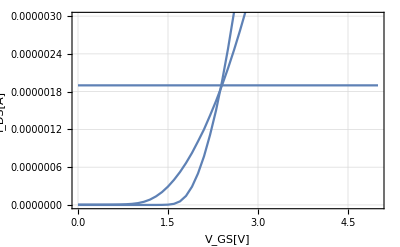

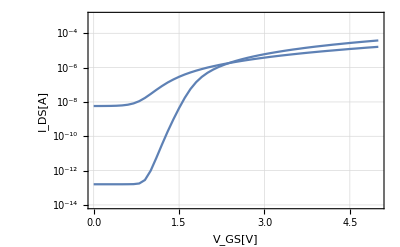

```mathematica
L37W6temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L37uW6u/temp30_ids.txt","Table"]];
L37W6logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L37uW6u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L37W6temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L37uW6u/temp300_ids.txt","Table"]];
L37W6logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L37uW6u/temp300_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L37W6stand=ListLinePlot[{{0,1.9 10^-6},{5,1.9 10^-6}}];
Show[L37W6stand,L37W6temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)L37W6temp300,PlotRange->{0,0.000003},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[L37W6logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)L37W6logtemp300,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

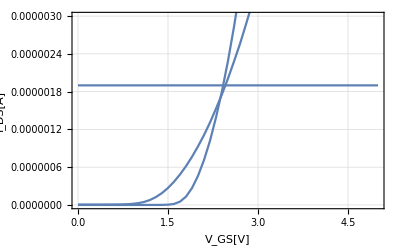

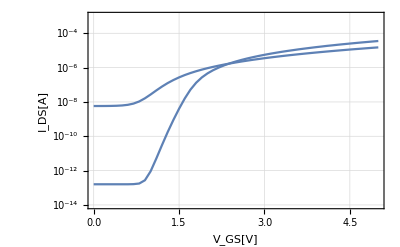

```mathematica
L40W6temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L40uW6u/temp30_ids.txt","Table"]];
L40W6logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L40uW6u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L40W6temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L40uW6u/temp300_ids.txt","Table"]];
L40W6logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L40uW6u/temp300_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L40W6stand=ListLinePlot[{{0,1.9 10^-6},{5,1.9 10^-6}}];
Show[L40W6stand,L40W6temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)L40W6temp300,PlotRange->{0,0.000003},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[L40W6logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)L40W6logtemp300,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

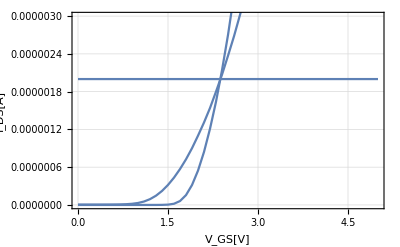

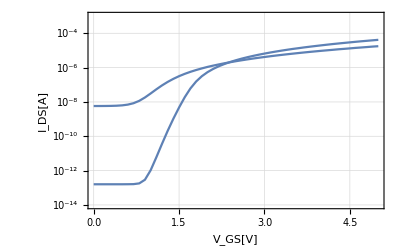

```mathematica
L34W6temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L34uW6u/temp30_ids.txt","Table"]];
L34W6logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L34uW6u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L34W6temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L34uW6u/temp300_ids.txt","Table"]];
L34W6logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L34uW6u/temp300_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
L34W6stand=ListLinePlot[{{0,2 10^-6},{5,2 10^-6}}];
Show[L34W6stand,L34W6temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)L34W6temp300,PlotRange->{0,0.000003},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[L34W6logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)L34W6logtemp300,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

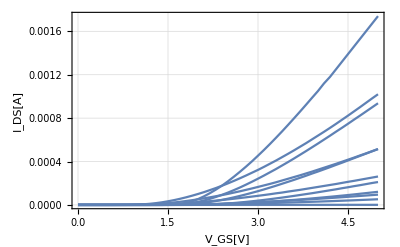

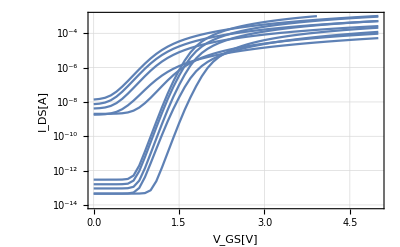

```mathematica
Show[W12temp30,W12temp300,W6temp30,W6temp300,W12stand,W3temp30,W3temp300,W1temp30,W1temp300,L3W1temp30,L3W1temp300,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
Show[W12logtemp30,W12logtemp300,W6logtemp30,W6logtemp300,W12stand,W3logtemp30,W3logtemp300,W1logtemp30,W1logtemp300,L3W1logtemp30,L3W1logtemp300,Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
```

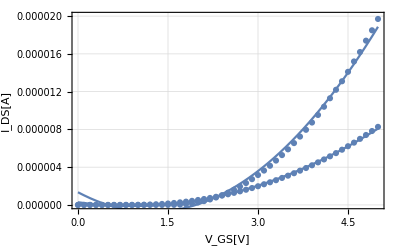

```mathematica
Show[{ListPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L24uW1u/temp30_ids.txt","Table"]],Plot[Evaluate[Fit[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L24uW1u/temp30_ids.txt","Table"],{1,x,x^2},x]],{x,0,5}],ListPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L24uW1u/temp300_ids.txt","Table"]],Plot[Evaluate[Fit[Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L24uW1u/temp300_ids.txt","Table"],{1,x,x^2},x]],{x,0,5}]},PlotRange->{0,0.00002},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]
(*Plot[{Evaluate[Fit[Import["D:/OneDrive/v3_0_3/htpsic/L24uW1u/temp30_ids.txt","Table"],{1,x,x^2},x]],Evaluate[Fit[Import["D:/OneDrive/v3_0_3/htpsic/L24uW1u/temp300_ids.txt","Table"],{1,x,x^2},x]]},{x,0,5},PlotRange->{{0,5},{0,5 10^-6}},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"],Style["I_DS[A]"]}]*)
```

```mathematica
Fit[Import["D:/OneDrive/v3_0_3/htpsic/L24uW1u/temp30_ids.txt","Table"],{1,x,x^2},x]
Fit[Import["D:/OneDrive/v3_0_3/htpsic/L24uW1u/temp300_ids.txt","Table"],{1,x,x^2},x]
```

1.34472×10^-6-3.39402×10^-6 x+1.37997×10^-6 x^2

2.84671×10^-7-8.72811×10^-7 x+4.86577×10^-7 x^2

When VDS = 1.5 V, current is lower.

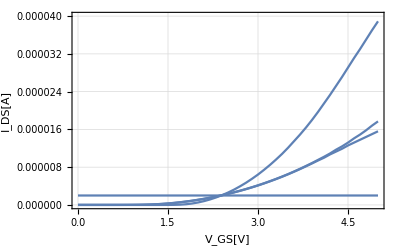

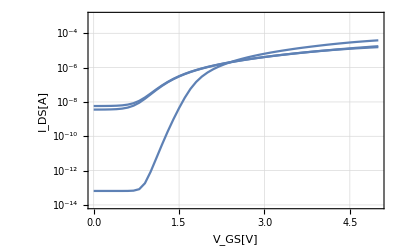

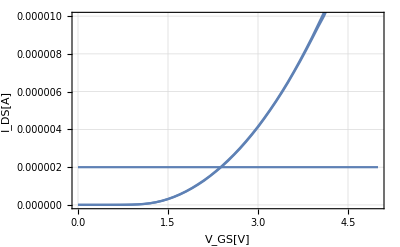

```mathematica
Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/nL34uW6u/temp30_ids.txt", "Table"];
Import["D:/OneDrive/v3_0_3/htpsic/vds5V/L34uW6u/temp30_ids.txt", "Table"];
vds15L34W6temp30 = ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/nL34uW6u/temp30_ids.txt", "Table"]];
vds15L34W6logtemp30 = ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/nL34uW6u/temp30_ids.txt", "Table"], Joined -> True, PlotRange -> {10^-14, 0.001}];
vds15L34W6temp300 = ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/nL34uW6u/temp300_ids.txt", "Table"]];
vds15L34W6logtemp300 = ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/nL34uW6u/temp300_ids.txt", "Table"], Joined -> True, PlotRange -> {10^-14, 0.001}];
vds15L34W6stand = ListLinePlot[{{0, 2 10^-6}, {5, 2 10^-6}}];
Show[vds15L34W6stand, vds15L34W6temp30, L34W6temp300,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)vds15L34W6temp300, PlotRange -> {0, 0.00004}, Frame -> True, GridLines -> Automatic, FrameLabel -> {Style["V_GS[V]"], Style["I_DS[A]"]}]
Show[vds15L34W6logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)vds15L34W6logtemp300, L34W6logtemp300, Frame -> True, GridLines -> Automatic, FrameLabel -> {Style["V_GS[V]"], Style["I_DS[A]"]}]
Show[vds15L34W6stand, vds15L34W6temp300, L34W6temp300,PlotRange -> {0, 0.00001}, Frame -> True, GridLines -> Automatic, FrameLabel -> {Style["V_GS[V]"], Style["I_DS[A]"]}]
```

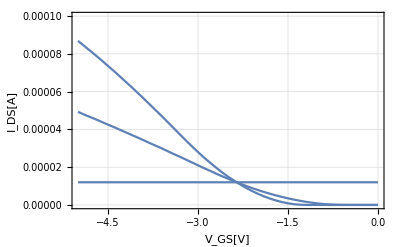

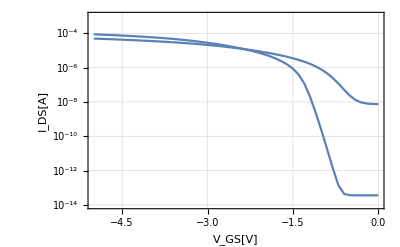

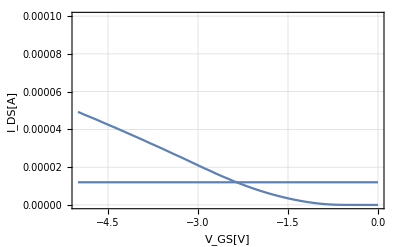

```mathematica
vds15pL6W6temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/pL6uW6u/temp30_ids.txt","Table"]];
vds15pL6W6logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/pL6uW6u/temp30_ids.txt","Table"], Joined -> True, PlotRange -> {10^-14, 0.001}];
vds15pL6W6temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/pL6uW6u/temp300_ids.txt","Table"]];
vds15pL6W6logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/pL6uW6u/temp300_ids.txt","Table"], Joined -> True, PlotRange -> {10^-14, 0.001}];
vds15pL6W6stand=ListLinePlot[{{0, 12 10^-6}, {-5,12 10^-6}}];
Show[vds15pL6W6stand,vds15pL6W6temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)vds15pL6W6temp300, PlotRange -> {0, 0.0001}, Frame -> True, GridLines -> Automatic, FrameLabel -> {Style["V_GS[V]"], Style["I_DS[A]"]}]
Show[vds15pL6W6logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)vds15pL6W6logtemp300, Frame -> True, GridLines -> Automatic, FrameLabel -> {Style["V_GS[V]"], Style["I_DS[A]"]}]
Show[vds15pL6W6stand,vds15pL6W6temp300,PlotRange->{0,0.0001},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"], Style["I_DS[A]"]}]
```

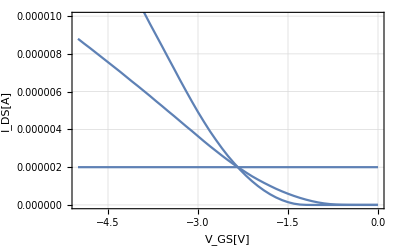

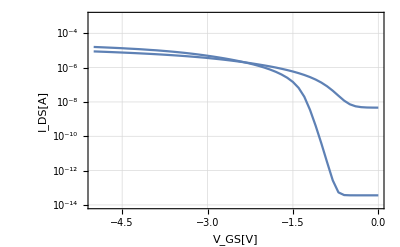

```mathematica
vds15pL34W6temp30=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/pL34uW6u/temp30_ids.txt","Table"]];
vds15pL34W6logtemp30=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/pL34uW6u/temp30_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
vds15pL34W6temp300=ListLinePlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/pL34uW6u/temp300_ids.txt","Table"]];
vds15pL34W6logtemp300=ListLogPlot[Import["D:/OneDrive/v3_0_3/htpsic/vds1p5V/pL34uW6u/temp300_ids.txt","Table"],Joined->True,PlotRange->{10^-14,0.001}];
vds15pL34W6stand=ListLinePlot[{{0,2 10^-6},{-5,2 10^-6}}];
Show[vds15pL34W6stand,vds15pL34W6temp30,(*temp80,*)(*L3W1temp130,*)(*temp180,*)(*L3W1temp230,*)(*temp280,*)vds15pL34W6temp300,PlotRange->{0,0.00001},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"], Style["I_DS[A]"]}]
Show[vds15pL34W6logtemp30,(*L3W1logtemp130,L3W1logtemp230,*)vds15pL34W6logtemp300, Frame -> True, GridLines -> Automatic, FrameLabel -> {Style["V_GS[V]"], Style["I_DS[A]"]}]
(*Show[vds15pL34W6stand,vds15pL34W6temp300,PlotRange->{0,0.0001},Frame->True,GridLines->Automatic,FrameLabel->{Style["V_GS[V]"], Style["I_DS[A]"]}]*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.341703

5580.6 (0.00105765-0.000172346 Log[0.00333333 T])

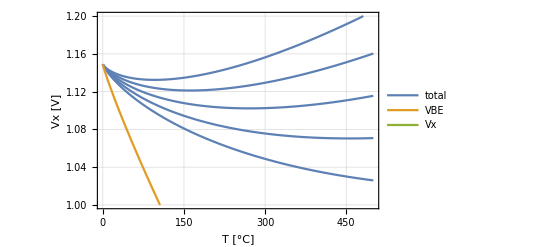

```mathematica
(*Is=Exp[0] 6.5 10^-8*)(* from c:\users\sia-cheng\onedrive\v3_0_3\core1\models\dio\tm\dn.mod *)RTIc=Is (Exp[(e RTVEB)/(kB T)]-1)/.Is->4 10^-12/.e->1.60218 10^-19/.kB->1.38065 10^-23/.T->300; (* forward current of a diode, backward saturation current is choosen according to HSPICE manual document *)
sol=Solve[RTIc==2.2 10^-6,RTVEB][[1,1,2]](* this "RTIc" value here is needed to be designed carefully *)
VBE[T_]:=RTVg+T/T0 (RTVEB-RTVg)+(η) (kB T)/e Log[T/T0]/.η->2/.RTVEB->0.78/.RTVg->1.149/.T0->300/.e->1.60218 10^-19/.kB->1.38065 10^-23(* this value "VBE" is considered here as 1st order of T, a linear function. In fact, it is not *)
(* Plot[VBE[T],{T,0,500}]*) (*use the command when needed *)
Vx[m_,T_]:=m Log[N] kB/e T/.N->8/.e->1.60218 10^-19/.kB->1.38065 10^-23  (* according to paper named "CMOS Bandgap References With Self-Biased Symmetrically Matched Current-Voltage Mirror and Extension of Sub-1-V Design", Lam YH et .al, Eq.25 *)
Manipulate[Plot[{VBE[T]+Vx[m,T],VBE[T],Vx[m,T]},{T,0,500},PlotRange->{{0,500},{.8,1.3}}],{{m,1,"ratio parameter (R5A + R5B)/R1"},1,10}]
Valuem=Solve[D[VBE[T]+Vx[m,T],T]==0,m][[1,1,2]](* calculation of the exact value of m *)
Plot[{Table[VBE[T]+Vx[m,T],{m,5,7,0.5}],VBE[T],Vx[5.5,T]},{T,0,500},PlotRange->{{0,500},{1,1.2}},Frame->True,GridLines->Automatic,FrameLabel->{Style[T"[°C]"],Style["Vx [V]"]},PlotLegends->{"total","VBE","Vx"}]
```

```mathematica
Do[i^2,{i,1,3,1}]
```

```mathematica
y[x_]:=SeriesData[x,0,Table[a[i],{i,0,7}]]
```

```mathematica
seriesDE=(y'[x])^2-y[x]==x
```

(-a[0]+a[1]^2)+(-a[1]+4 a[1] a[2]) x+(-a[2]+4 a[2]^2+6 a[1] a[3]) x^2+(-a[3]+12 a[2] a[3]+8 a[1] a[4]) x^3+(9 a[3]^2-a[4]+16 a[2] a[4]+10 a[1] a[5]) x^4+(24 a[3] a[4]-a[5]+20 a[2] a[5]+12 a[1] a[6]) x^5+(16 a[4]^2+30 a[3] a[5]-a[6]+24 a[2] a[6]+14 a[1] a[7]) x^6+O[x]^7==x

```mathematica
coeffEqn=LogicalExpand[seriesDE]
```

-a[0]+a[1]^2==0&&-1-a[1]+4 a[1] a[2]==0&&-a[2]+4 a[2]^2+6 a[1] a[3]==0&&-a[3]+12 a[2] a[3]+8 a[1] a[4]==0&&9 a[3]^2-a[4]+16 a[2] a[4]+10 a[1] a[5]==0&&24 a[3] a[4]-a[5]+20 a[2] a[5]+12 a[1] a[6]==0&&16 a[4]^2+30 a[3] a[5]-a[6]+24 a[2] a[6]+14 a[1] a[7]==0

```mathematica
coeffSol=Solve[{coeffEqn,a[0]==1}]
```

{{a[0]→1,a[1]→1,a[2]→1/2,a[3]→-1/12,a[4]→5/96,a[5]→-41/960,a[6]→469/11520,a[7]→-6889/161280},{a[0]→1,a[1]→-1,a[2]→0,a[3]→0,a[4]→0,a[5]→0,a[6]→0,a[7]→0}}

```mathematica
y[x]/.Join[coeffSol]//Normal
```

{1+x+x^2/2-x^3/12+(5 x^4)/96-(41 x^5)/960+(469 x^6)/11520-(6889 x^7)/161280,1-x}